```mathematica
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","NuclideChart"}];
```

#### Animation

```mathematica
zmin=1;
zmax=45 (*26*);
factor=1.0;
amin=Min[IsotopeData[zmin,"MassNumber"]]-zmin*1;
amax=Max[IsotopeData[zmax,"MassNumber"]]-zmax*1;
g=Quiet@Table[IsotopeData[{z,a},"BindingEnergy"],{z,zmin,zmax},{a,amin,amax}];
MaxBindingEnergy=Max[Cases[Flatten[g],_Real]];
gInv=Quiet@Table[factor*(MaxBindingEnergy-IsotopeData[{z,a},"BindingEnergy"]),{z,zmin,zmax},{a,amin,amax}];
```

```mathematica
gr=Quiet@ListPlot3D[gInv,
InterpolationOrder->0,
Mesh->None,
BoxRatios->Automatic,
PlotRange->All,
AspectRatio->2,
Filling->Axis,
Ticks->None,
FillingStyle->Directive[LightGray,Opacity[0.50]],
PlotStyle->Directive[Opacity[0.75]],
ColorFunction->"Rainbow",
ImageSize->{1000,600},
PreserveImageOptions->False,
RotationAction->"Clip"
];
```

```mathematica
Animate[
With[{v=RotationTransform[θ,{0,0,1}][4.5*{1,0,0.2}]},
Column[{
Graphics3D[{Red,PointSize[Large],Point[v],Line[{v,{0,0,0}}],Black,PointSize[Large],Point[{0,0,0}]},PlotRange->2],
Show[gr,ViewPoint->v,ViewAngle->4.5°,RotationAction->"Clip"],
Dynamic[v]
}]],
{θ,0.25Pi,2.25Pi},
AnimationRunning->True]
```

```mathematica
oneFrame[θ_]:=Module[{v,a=4°,d=4.5},
v=RotationTransform[θ,{0,0,1}][d*{1,0,0.2}];
Show[Show[gr,ViewPoint->v,ViewAngle->a,RotationAction->"Clip"]]
];
```

```mathematica
oneFrame[-0.15Pi];
```

```mathematica
360/72.
```

5.

```mathematica
allFrame=Module[{nbFrame=72},
Table[oneFrame[(i/nbFrame)*2Pi],{i,nbFrame}]
];
```

```mathematica
name="rotatingNuclide3DChart";
Export[FileNameJoin[{repoDir,"Pictures",name<>".gif"}],allFrame,ImageSize->Automatic,"DisplayDurations"->0.1];
```

#### Graphs

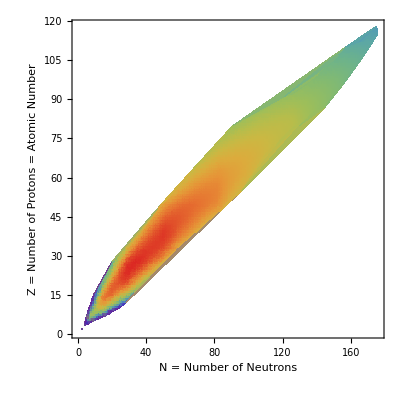

```mathematica
g1=Table[{a-z,z,IsotopeData[{z,a},"BindingEnergy"]},{z,1,118},{a,IsotopeData[z,"MassNumber"]}]//Flatten[#,1]&;
ListDensityPlot[g1,FrameLabel->{"N = Number of Neutrons","Z = Number of Protons = Atomic Number"},ColorFunction->"Rainbow"]
```

```mathematica
isotopeDataBindingEnergy[z_,a_]:=Module[{t},
t=Quiet@IsotopeData[{z,a},"BindingEnergy"];
If[NumericQ[t],t,0]
];
g2=Table[isotopeDataBindingEnergy[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
legend1=Rasterize@Graphics[Legend[ColorData["Rainbow"][1-#1]&,10,"High","Low",LegendShadow->None],ImageSize->50,ImagePadding->0]
```

-Graphics-

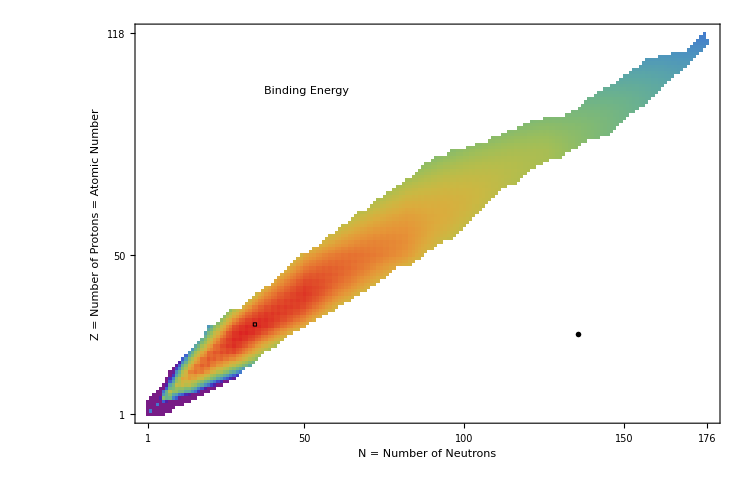

```mathematica
output=ArrayPlot[g2,DataReversed->True,ColorRules->{0->White},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{6.5,8.8},{0,1}]]&),AspectRatio->Automatic,Frame->True,FrameTicks->All,ImageSize->750,Mesh->0,PixelConstrained->False,FrameLabel->(Text@Style[#,Bold,14]&)/@{"Z = Number of Protons = Atomic Number","N = Number of Neutrons"},Epilog->{{EdgeForm[Black],Opacity[0],Rectangle[{34-0.5,28-0.5},{34+0.5,28+0.5}]},Inset[legend1,{135,25}],Inset[Text@Style["Binding Energy",Bold,20],{50,100}]}]
```

```mathematica
name="bindingEnergyNuclide";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
isotopeDataStable[z_,a_]:=Module[{t},
t=Quiet@IsotopeData[{z,a},"Stable"];
If[NumberQ[Boole[t]],Boole[t],-1]
];
g3=Table[isotopeDataStable[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
legendPlot[colorList_,labelList_]:=Module[{t},
t=Table[{Graphics[{colorList[[i]],Rectangle[{-1,-1},{1,1}]},ImageSize->15]," ",Text@Style[labelList[[i]],12,Bold]},{i,Length[colorList]}];
(*Framed[Column[Map[Row,t]]]*)
Column[Map[Row,t]]
];
```

```mathematica
colorList={Darker[Blue,0.7],Lighter[Blue,0.4]};
labelList={"Stable","Unstable"};
legend2=legendPlot[colorList,labelList]
```

-Graphics- Stable
-Graphics- Unstable

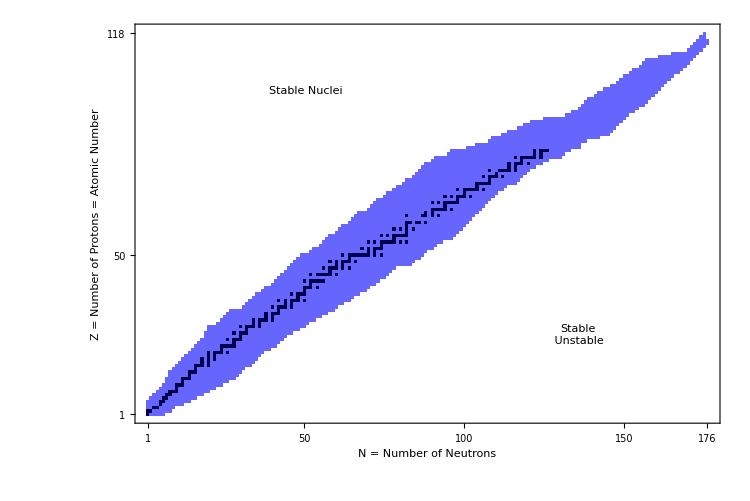

```mathematica
output=ArrayPlot[g3,DataReversed->True,ColorRules->{1->Darker[Blue,0.7],0->Lighter[Blue,0.4],-1->White},ColorFunction->"Rainbow",AspectRatio->Automatic,Frame->True,FrameTicks->All,ImageSize->750,Mesh->0,PixelConstrained->False,FrameLabel->(Text@Style[#,Bold,14]&)/@{"Z = Number of Protons = Atomic Number","N = Number of Neutrons"},Epilog->{Inset[legend2,{135,25}],Inset[Text@Style["Stable Nuclei",Bold,20],{50,100}]}]
```

```mathematica
name="stableNuclide";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
isotopeDataDecayModes[z_,a_]:=Module[{t,u,output},
t=Quiet@IsotopeData[{z,a},"DecayModes"];
u=Quiet@IsotopeData[{z,a},"Stable"];
If[!VectorQ[t],
output=-1,
If[Length[t]≥1,
output=Which[
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"BetaPlusDecay","BetaPlusDelayed"~~__,"ElectronCapture","DoubleBetaPlusDecay","PositronEmission"}],1,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{___~~"ProtonEmission"}],2,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"BetaDecay","BetaDelayed"~~__,"DoubleBetaDecay"}],3,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{___~~"NeutronEmission"}],4,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"AlphaEmission"}],5,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"SpontaneousFission"}],6,
True,7
]
];
If[u==True,output=0]
];
output
];
g4=Table[isotopeDataDecayModes[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
colorList={Black,Lighter[Blue,0.5], Magenta,Orange,Red,Yellow,Green};
labelList={"Stable","β+","Proton Emission","β-","Neutron Emission","α","Spontaneous Fission"};
legend3=legendPlot[colorList,labelList]
```

-Graphics- Stable
-Graphics- β+
-Graphics- Proton Emission
-Graphics- β-
-Graphics- Neutron Emission
-Graphics- α
-Graphics- Spontaneous Fission

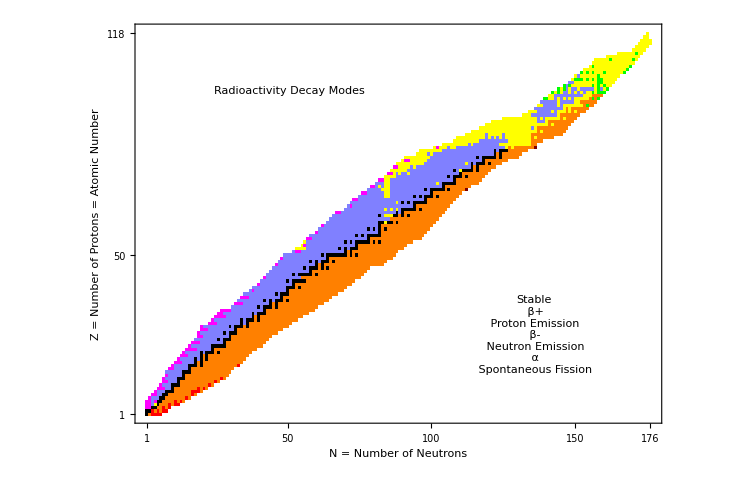

```mathematica
output=ArrayPlot[g4,DataReversed->True,ColorRules->{-1->White,0->Black,1->Lighter[Blue,0.5], 2->Magenta,3->Orange,4->Red,5->Yellow,6->Green,7->Gray},AspectRatio->Automatic,Frame->True,FrameTicks->All,ImageSize->750,Mesh->0,PixelConstrained->False,FrameLabel->(Text@Style[#,Bold,14]&)/@{"Z = Number of Protons = Atomic Number","N = Number of Neutrons"},Epilog->{Inset[legend3,{135,25}],Inset[Text@Style["Radioactivity Decay Modes",Bold,20],{50,100}]}]
```

```mathematica
name="radioactivityNuclide";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
(*is=Select[IsotopeData[],100≤IsotopeData[#,"MassNumber"]≤102&];
LayeredGraphPlot[Table[(IsotopeData[#,"FullSymbol"]&/@(i->#))&/@IsotopeData[i,"DaughterNuclides"],{i,is}]//Flatten,AspectRatio->0.75,DirectedEdges->True,VertexLabeling->True,ImageSize->700]*)
```

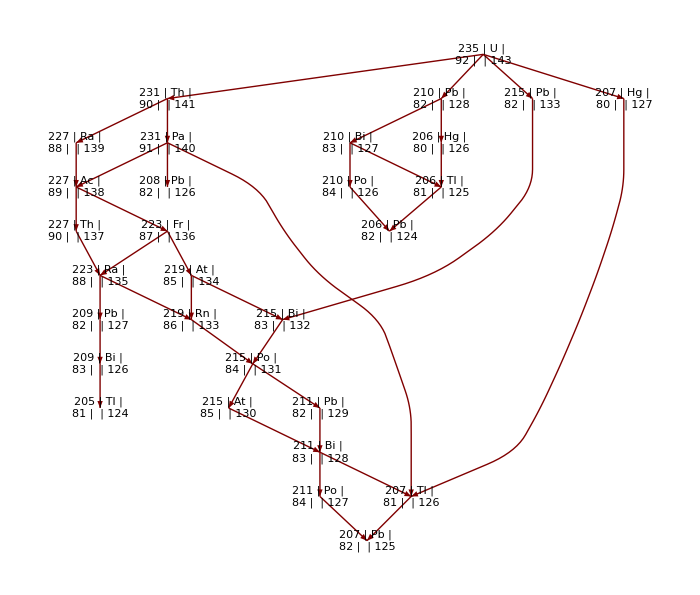

```mathematica
DaughterNuclides[s_List]:=DeleteCases[Union[Apply[Join,Map[IsotopeData[#,"DaughterNuclides"]&,DeleteCases[s,_Missing]]]],_Missing];
ReachableNuclides[s_List]:=FixedPoint[Union[Join[#,DaughterNuclides[#]]]&,s];
DecayNetwork[iso_List]:=Apply[Join,Map[Thread[#->DaughterNuclides[{#}]]&,ReachableNuclides[iso]]];
DecayNetworkPlot[s_]:=LayeredGraphPlot[Map[IsotopeData[#,"FullSymbol"]&,DecayNetwork[{s}],{2}],VertexLabeling->True,(*VertexRenderingFunction->(Text[Framed[Style[#2,8],Background->LightYellow],#1]&),*)ImageSize->{700,700},AspectRatio->0.85,DirectedEdges->True];

output=DecayNetworkPlot["Uranium235"]
```

```mathematica
name="u235DecayGraph";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
tabStable=Table[{z,ElementData[z,"Name"],Map[(IsotopeData[{z,#},"FullSymbol"]&),ElementData[z,"StableIsotopes"]]},{z,118}];
```

```mathematica
tabStable[[1;;5]]
```

{{1,hydrogen,{1 | H | 
1 |  | 0,2 | H | 
1 |  | 1}},{2,helium,{3 | He | 
2 |  | 1,4 | He | 
2 |  | 2}},{3,lithium,{6 | Li | 
3 |  | 3,7 | Li | 
3 |  | 4}},{4,beryllium,{9 | Be | 
4 |  | 5}},{5,boron,{10 | B | 
5 |  | 5,11 | B | 
5 |  | 6}}}

```mathematica
output=Column[{
Text@Style["Stable Nuclei (1≤ Z ≤41)",14,Bold],
"\n",
Grid[
Map[Text,
Prepend[Table[{tabStable[[z,1]],tabStable[[z,2]],Length[tabStable[[z,3]]],Row[Riffle[tabStable[[z,3]],"  "]]},{z,1,41}],
(Style[#,Bold]&)/@{"Z","Element Name","Nb of Stable Isotopes","Stable Isotopes"}],
{2}],
(*Dividers->{{{False}},{2->Black}},*)
Dividers->{{2->Black},{2->Black}},
Background->{None,{{None,LightRed}}},
Alignment->Left,
Spacings->{1.5,0.15}
]
},Center]
name="stableIsotope1";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];

output=Column[{
Text@Style["Stable Nuclei (42 ≤ Z)",14,Bold],
"\n",
Grid[
Map[Text,
Prepend[Table[{tabStable[[z,1]],tabStable[[z,2]],Length[tabStable[[z,3]]],Row[Riffle[tabStable[[z,3]],"  "]]},{z,42,82}],
(Style[#,Bold]&)/@{"Z","Element Name","Nb of Stable Isotopes","Stable Isotopes"}],
{2}],
(*Dividers->{{{False}},{2->Black}},*)
Dividers->{{2->Black},{2->Black}},
Background->{None,{{None,LightRed}}},
Alignment->Left,
Spacings->{1.5,0.15}
]
},Center]
name="stableIsotope2";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

Stable Nuclei (1≤ Z ≤41)


Z | Element Name | Nb of Stable Isotopes | Stable Isotopes
1 | hydrogen | 2 | 1 | H | 
1 |  | 0  2 | H | 
1 |  | 1
2 | helium | 2 | 3 | He | 
2 |  | 1  4 | He | 
2 |  | 2
3 | lithium | 2 | 6 | Li | 
3 |  | 3  7 | Li | 
3 |  | 4
4 | beryllium | 1 | 9 | Be | 
4 |  | 5
5 | boron | 2 | 10 | B | 
5 |  | 5  11 | B | 
5 |  | 6
6 | carbon | 2 | 12 | C | 
6 |  | 6  13 | C | 
6 |  | 7
7 | nitrogen | 2 | 14 | N | 
7 |  | 7  15 | N | 
7 |  | 8
8 | oxygen | 3 | 16 | O | 
8 |  | 8  17 | O | 
8 |  | 9  18 | O | 
8 |  | 10
9 | fluorine | 1 | 19 | F | 
9 |  | 10
10 | neon | 3 | 20 | Ne | 
10 |  | 10  21 | Ne | 
10 |  | 11  22 | Ne | 
10 |  | 12
11 | sodium | 1 | 23 | Na | 
11 |  | 12
12 | magnesium | 3 | 24 | Mg | 
12 |  | 12  25 | Mg | 
12 |  | 13  26 | Mg | 
12 |  | 14
13 | aluminum | 1 | 27 | Al | 
13 |  | 14
14 | silicon | 3 | 28 | Si | 
14 |  | 14  29 | Si | 
14 |  | 15  30 | Si | 
14 |  | 16
15 | phosphorus | 1 | 31 | P | 
15 |  | 16
16 | sulfur | 4 | 32 | S | 
16 |  | 16  33 | S | 
16 |  | 17  34 | S | 
16 |  | 18  36 | S | 
16 |  | 20
17 | chlorine | 2 | 35 | Cl | 
17 |  | 18  37 | Cl | 
17 |  | 20
18 | argon | 3 | 36 | Ar | 
18 |  | 18  38 | Ar | 
18 |  | 20  40 | Ar | 
18 |  | 22
19 | potassium | 2 | 39 | K | 
19 |  | 20  41 | K | 
19 |  | 22
20 | calcium | 5 | 40 | Ca | 
20 |  | 20  42 | Ca | 
20 |  | 22  43 | Ca | 
20 |  | 23  44 | Ca | 
20 |  | 24  46 | Ca | 
20 |  | 26
21 | scandium | 1 | 45 | Sc | 
21 |  | 24
22 | titanium | 5 | 46 | Ti | 
22 |  | 24  47 | Ti | 
22 |  | 25  48 | Ti | 
22 |  | 26  49 | Ti | 
22 |  | 27  50 | Ti | 
22 |  | 28
23 | vanadium | 1 | 51 | V | 
23 |  | 28
24 | chromium | 4 | 50 | Cr | 
24 |  | 26  52 | Cr | 
24 |  | 28  53 | Cr | 
24 |  | 29  54 | Cr | 
24 |  | 30
25 | manganese | 1 | 55 | Mn | 
25 |  | 30
26 | iron | 4 | 54 | Fe | 
26 |  | 28  56 | Fe | 
26 |  | 30  57 | Fe | 
26 |  | 31  58 | Fe | 
26 |  | 32
27 | cobalt | 1 | 59 | Co | 
27 |  | 32
28 | nickel | 5 | 58 | Ni | 
28 |  | 30  60 | Ni | 
28 |  | 32  61 | Ni | 
28 |  | 33  62 | Ni | 
28 |  | 34  64 | Ni | 
28 |  | 36
29 | copper | 2 | 63 | Cu | 
29 |  | 34  65 | Cu | 
29 |  | 36
30 | zinc | 5 | 64 | Zn | 
30 |  | 34  66 | Zn | 
30 |  | 36  67 | Zn | 
30 |  | 37  68 | Zn | 
30 |  | 38  70 | Zn | 
30 |  | 40
31 | gallium | 2 | 69 | Ga | 
31 |  | 38  71 | Ga | 
31 |  | 40
32 | germanium | 4 | 70 | Ge | 
32 |  | 38  72 | Ge | 
32 |  | 40  73 | Ge | 
32 |  | 41  74 | Ge | 
32 |  | 42
33 | arsenic | 1 | 75 | As | 
33 |  | 42
34 | selenium | 5 | 74 | Se | 
34 |  | 40  76 | Se | 
34 |  | 42  77 | Se | 
34 |  | 43  78 | Se | 
34 |  | 44  80 | Se | 
34 |  | 46
35 | bromine | 2 | 79 | Br | 
35 |  | 44  81 | Br | 
35 |  | 46
36 | krypton | 6 | 78 | Kr | 
36 |  | 42  80 | Kr | 
36 |  | 44  82 | Kr | 
36 |  | 46  83 | Kr | 
36 |  | 47  84 | Kr | 
36 |  | 48  86 | Kr | 
36 |  | 50
37 | rubidium | 1 | 85 | Rb | 
37 |  | 48
38 | strontium | 4 | 84 | Sr | 
38 |  | 46  86 | Sr | 
38 |  | 48  87 | Sr | 
38 |  | 49  88 | Sr | 
38 |  | 50
39 | yttrium | 1 | 89 | Y | 
39 |  | 50
40 | zirconium | 4 | 90 | Zr | 
40 |  | 50  91 | Zr | 
40 |  | 51  92 | Zr | 
40 |  | 52  94 | Zr | 
40 |  | 54
41 | niobium | 1 | 93 | Nb | 
41 |  | 52

Stable Nuclei (42 ≤ Z)


Z | Element Name | Nb of Stable Isotopes | Stable Isotopes
42 | molybdenum | 6 | 92 | Mo | 
42 |  | 50  94 | Mo | 
42 |  | 52  95 | Mo | 
42 |  | 53  96 | Mo | 
42 |  | 54  97 | Mo | 
42 |  | 55  98 | Mo | 
42 |  | 56
43 | technetium | 0 | 
44 | ruthenium | 7 | 100 | Ru | 
44 |  | 56  101 | Ru | 
44 |  | 57  102 | Ru | 
44 |  | 58  104 | Ru | 
44 |  | 60  96 | Ru | 
44 |  | 52  98 | Ru | 
44 |  | 54  99 | Ru | 
44 |  | 55
45 | rhodium | 1 | 103 | Rh | 
45 |  | 58
46 | palladium | 6 | 102 | Pd | 
46 |  | 56  104 | Pd | 
46 |  | 58  105 | Pd | 
46 |  | 59  106 | Pd | 
46 |  | 60  108 | Pd | 
46 |  | 62  110 | Pd | 
46 |  | 64
47 | silver | 2 | 107 | Ag | 
47 |  | 60  109 | Ag | 
47 |  | 62
48 | cadmium | 6 | 106 | Cd | 
48 |  | 58  108 | Cd | 
48 |  | 60  110 | Cd | 
48 |  | 62  111 | Cd | 
48 |  | 63  112 | Cd | 
48 |  | 64  114 | Cd | 
48 |  | 66
49 | indium | 1 | 113 | In | 
49 |  | 64
50 | tin | 10 | 112 | Sn | 
50 |  | 62  114 | Sn | 
50 |  | 64  115 | Sn | 
50 |  | 65  116 | Sn | 
50 |  | 66  117 | Sn | 
50 |  | 67  118 | Sn | 
50 |  | 68  119 | Sn | 
50 |  | 69  120 | Sn | 
50 |  | 70  122 | Sn | 
50 |  | 72  124 | Sn | 
50 |  | 74
51 | antimony | 2 | 121 | Sb | 
51 |  | 70  123 | Sb | 
51 |  | 72
52 | tellurium | 5 | 120 | Te | 
52 |  | 68  122 | Te | 
52 |  | 70  124 | Te | 
52 |  | 72  125 | Te | 
52 |  | 73  126 | Te | 
52 |  | 74
53 | iodine | 1 | 127 | I | 
53 |  | 74
54 | xenon | 9 | 124 | Xe | 
54 |  | 70  126 | Xe | 
54 |  | 72  128 | Xe | 
54 |  | 74  129 | Xe | 
54 |  | 75  130 | Xe | 
54 |  | 76  131 | Xe | 
54 |  | 77  132 | Xe | 
54 |  | 78  134 | Xe | 
54 |  | 80  136 | Xe | 
54 |  | 82
55 | cesium | 1 | 133 | Cs | 
55 |  | 78
56 | barium | 7 | 130 | Ba | 
56 |  | 74  132 | Ba | 
56 |  | 76  134 | Ba | 
56 |  | 78  135 | Ba | 
56 |  | 79  136 | Ba | 
56 |  | 80  137 | Ba | 
56 |  | 81  138 | Ba | 
56 |  | 82
57 | lanthanum | 1 | 139 | La | 
57 |  | 82
58 | cerium | 4 | 136 | Ce | 
58 |  | 78  138 | Ce | 
58 |  | 80  140 | Ce | 
58 |  | 82  142 | Ce | 
58 |  | 84
59 | praseodymium | 1 | 141 | Pr | 
59 |  | 82
60 | neodymium | 5 | 142 | Nd | 
60 |  | 82  143 | Nd | 
60 |  | 83  145 | Nd | 
60 |  | 85  146 | Nd | 
60 |  | 86  148 | Nd | 
60 |  | 88
61 | promethium | 0 | 
62 | samarium | 5 | 144 | Sm | 
62 |  | 82  149 | Sm | 
62 |  | 87  150 | Sm | 
62 |  | 88  152 | Sm | 
62 |  | 90  154 | Sm | 
62 |  | 92
63 | europium | 2 | 151 | Eu | 
63 |  | 88  153 | Eu | 
63 |  | 90
64 | gadolinium | 6 | 154 | Gd | 
64 |  | 90  155 | Gd | 
64 |  | 91  156 | Gd | 
64 |  | 92  157 | Gd | 
64 |  | 93  158 | Gd | 
64 |  | 94  160 | Gd | 
64 |  | 96
65 | terbium | 1 | 159 | Tb | 
65 |  | 94
66 | dysprosium | 7 | 156 | Dy | 
66 |  | 90  158 | Dy | 
66 |  | 92  160 | Dy | 
66 |  | 94  161 | Dy | 
66 |  | 95  162 | Dy | 
66 |  | 96  163 | Dy | 
66 |  | 97  164 | Dy | 
66 |  | 98
67 | holmium | 1 | 165 | Ho | 
67 |  | 98
68 | erbium | 6 | 162 | Er | 
68 |  | 94  164 | Er | 
68 |  | 96  166 | Er | 
68 |  | 98  167 | Er | 
68 |  | 99  168 | Er | 
68 |  | 100  170 | Er | 
68 |  | 102
69 | thulium | 1 | 169 | Tm | 
69 |  | 100
70 | ytterbium | 7 | 168 | Yb | 
70 |  | 98  170 | Yb | 
70 |  | 100  171 | Yb | 
70 |  | 101  172 | Yb | 
70 |  | 102  173 | Yb | 
70 |  | 103  174 | Yb | 
70 |  | 104  176 | Yb | 
70 |  | 106
71 | lutetium | 1 | 175 | Lu | 
71 |  | 104
72 | hafnium | 5 | 176 | Hf | 
72 |  | 104  177 | Hf | 
72 |  | 105  178 | Hf | 
72 |  | 106  179 | Hf | 
72 |  | 107  180 | Hf | 
72 |  | 108
73 | tantalum | 1 | 181 | Ta | 
73 |  | 108
74 | tungsten | 5 | 180 | W | 
74 |  | 106  182 | W | 
74 |  | 108  183 | W | 
74 |  | 109  184 | W | 
74 |  | 110  186 | W | 
74 |  | 112
75 | rhenium | 1 | 185 | Re | 
75 |  | 110
76 | osmium | 6 | 184 | Os | 
76 |  | 108  187 | Os | 
76 |  | 111  188 | Os | 
76 |  | 112  189 | Os | 
76 |  | 113  190 | Os | 
76 |  | 114  192 | Os | 
76 |  | 116
77 | iridium | 2 | 191 | Ir | 
77 |  | 114  193 | Ir | 
77 |  | 116
78 | platinum | 5 | 192 | Pt | 
78 |  | 114  194 | Pt | 
78 |  | 116  195 | Pt | 
78 |  | 117  196 | Pt | 
78 |  | 118  198 | Pt | 
78 |  | 120
79 | gold | 1 | 197 | Au | 
79 |  | 118
80 | mercury | 7 | 196 | Hg | 
80 |  | 116  198 | Hg | 
80 |  | 118  199 | Hg | 
80 |  | 119  200 | Hg | 
80 |  | 120  201 | Hg | 
80 |  | 121  202 | Hg | 
80 |  | 122  204 | Hg | 
80 |  | 124
81 | thallium | 2 | 203 | Tl | 
81 |  | 122  205 | Tl | 
81 |  | 124
82 | lead | 4 | 204 | Pb | 
82 |  | 122  206 | Pb | 
82 |  | 124  207 | Pb | 
82 |  | 125  208 | Pb | 
82 |  | 126

#### Testing Zone

```mathematica
Max[Flatten[g2]]
```

8.794549

```mathematica
IsotopeData[28,"Name"]
IsotopeData[{28,62},"BindingEnergy"]
IsotopeData[{28,62},"Name"]
IsotopeData[{28,62},"FullSymbol"]
IsotopeData[{28,62},"Stable"]
```

{nickel-48,nickel-49,nickel-50,nickel-51,nickel-52,nickel-53,nickel-54,nickel-55,nickel-56,nickel-57,nickel-58,nickel-59,nickel-60,nickel-61,nickel-62,nickel-63,nickel-64,nickel-65,nickel-66,nickel-67,nickel-68,nickel-69,nickel-70,nickel-71,nickel-72,nickel-73,nickel-74,nickel-75,nickel-76,nickel-77,nickel-78}

8.794549

nickel-62

62 | Ni | 
28 |  | 34

True

```mathematica
Transpose[{IsotopeData[26,"NeutronNumber"],IsotopeData[26,"Stable"]}]
```

{{19,False},{20,False},{21,False},{22,False},{23,False},{24,False},{25,False},{26,False},{27,False},{28,True},{29,False},{30,True},{31,True},{32,True},{33,False},{34,False},{35,False},{36,False},{37,False},{38,False},{39,False},{40,False},{41,False},{42,False},{43,False},{44,False},{45,False},{46,False}}

```mathematica
IsotopeData[{2,4},"FullSymbol"]
IsotopeData[{2,4},"Name"]
```

4 | He | 
2 |  | 2

helium-4

```mathematica
ta=Flatten@Table[IsotopeData[z,"Name"],{z,118}];
```

```mathematica
ta[[1;;150]];
Length[ta]
```

3181

```mathematica
nbDecayMode[z_,a_]:=Module[{t,output},
t=Quiet@IsotopeData[{z,a},"DecayModes"];
If[!VectorQ[t],Length[t],0]
];
```

```mathematica
nbDecayModePerIsotope=Table[nbDecayMode[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
N@Mean@Flatten@nbDecayModePerIsotope
```

1.45079

```mathematica
allDecayMode=SortBy[Tally[Flatten[Table[IsotopeData[z,"DecayModes"],{z,118}]]],Last];
Length[allDecayMode]
Total[allDecayMode[[All,2]]]
Total[allDecayMode[[25;;]][[All,2]]]
```

43

4490

4442

```mathematica
allDecayMode[[25;;]]
```

{{TwoNeutronEmission,8},{BetaPlusDelayedTwoProtonEmission,9},{BetaDelayedAlphaEmission,10},{PositronEmission,11},{BetaPlusDelayedFission,14},{TwoProtonEmission,16},{BetaDelayedTwoNeutronEmission,21},{NeutronEmission,24},{BetaPlusDelayedAlphaEmission,36},{DoubleBetaDecay,42},{DoubleBetaPlusDecay,46},{ProtonEmission,97},{ElectronCapture,147},{BetaPlusDelayedProtonEmission,200},{SpontaneousFission,203},{BetaDelayedNeutronEmission,316},{AlphaEmission,830},{BetaDecay,1190},{BetaPlusDecay,1222}}

```mathematica
IsotopeData["Classes"]
```

{AlphaEmission,BetaDecay,BetaDelayedAlphaEmission,BetaDelayedDeuteronEmission,BetaDelayedFission,BetaDelayedFourNeutronEmission,BetaDelayedNeutronAlphaEmission,BetaDelayedNeutronEmission,BetaDelayedThreeNeutronEmission,BetaDelayedTritonEmission,BetaDelayedTwoNeutronEmission,BetaPlusDecay,BetaPlusDelayedAlphaEmission,BetaPlusDelayedFission,BetaPlusDelayedProtonAlphaEmission,BetaPlusDelayedProtonEmission,BetaPlusDelayedThreeProtonEmission,BetaPlusDelayedTwoProtonEmission,Boson,Carbon12ClusterEmission,Carbon14ClusterEmission,DoubleBetaDecay,DoubleBetaPlusDecay,ElectronCapture,Fermion,Fluorine23ClusterEmission,Magnesium28ClusterEmission,Magnesium28Magnesium30ClusterEmission,Magnesium30ClusterEmission,Neon20ClusterEmission,Neon22ClusterEmission,Neon24ClusterEmission,Neon24Neon26ClusterEmission,Neon25ClusterEmission,NeutronEmission,Oxygen18ClusterEmission,Oxygen20ClusterEmission,PositronEmission,ProtonEmission,Silicon32ClusterEmission,Silicon34ClusterEmission,SpontaneousFission,Stable,ThreeNeutronEmission,TwoNeutronEmission,TwoProtonEmission,Unstable}

```mathematica
t=Table[Length[IsotopeData[z,"MassNumber"]],{z,118}]
```

{7,9,10,12,14,15,16,17,18,19,20,22,22,23,23,24,24,24,24,24,25,26,26,26,26,28,29,31,29,30,31,32,33,30,31,32,32,33,33,33,33,33,34,34,34,34,38,38,39,39,37,38,37,38,40,40,39,39,39,38,38,38,38,36,36,36,36,35,35,35,35,36,36,35,35,35,36,37,37,40,37,38,36,33,31,34,34,33,31,30,29,26,20,20,19,20,20,20,19,19,18,17,16,16,16,16,16,15,15,15,12,9,5,5,5,4,2,1}

```mathematica
t1=Table[{IsotopeData[z,"Name"],IsotopeData[z,"MassNumber"],IsotopeData[z,"AtomicNumber"],IsotopeData[z,"MassNumber"]-IsotopeData[z,"AtomicNumber"]},{z,113,118}]//Column
```

{{ununtrium-283,ununtrium-284,ununtrium-285,ununtrium-286,ununtrium-287},{283,284,285,286,287},{113,113,113,113,113},{170,171,172,173,174}}
{{ununquadium-285,ununquadium-286,ununquadium-287,ununquadium-288,ununquadium-289},{285,286,287,288,289},{114,114,114,114,114},{171,172,173,174,175}}
{{ununpentium-287,ununpentium-288,ununpentium-289,ununpentium-290,ununpentium-291},{287,288,289,290,291},{115,115,115,115,115},{172,173,174,175,176}}
{{ununhexium-289,ununhexium-290,ununhexium-291,ununhexium-292},{289,290,291,292},{116,116,116,116},{173,174,175,176}}
{{ununseptium-291,ununseptium-292},{291,292},{117,117},{174,175}}
{{ununoctium-293},{293},{118},{175}}

```mathematica
zmin=1;
zmax=118;
t2=Module[{t},
t=Table[If[NumberQ@Quiet@IsotopeData[{z,a},"MassNumber"],{z,a-z,a,IsotopeData[{z,a},"Name"],IsotopeData[{z,a},"FullSymbol"],IsotopeData[{z,a},"Stable"]},0],{z,zmin,zmax},{a,Min[IsotopeData[z,"MassNumber"]],Max[IsotopeData[z,"MassNumber"]]}];
t
];
```

```mathematica
t2[[27;;28]];
```

```mathematica
t3=Select[Flatten[t2,1],#[[6]]==True&];
Length[t3]
```

256

```mathematica
t3[[-5;;]]
```

{{81,124,205,thallium-205,205 | Tl | 
81 |  | 124,True},{82,122,204,lead-204,204 | Pb | 
82 |  | 122,True},{82,124,206,lead-206,206 | Pb | 
82 |  | 124,True},{82,125,207,lead-207,207 | Pb | 
82 |  | 125,True},{82,126,208,lead-208,208 | Pb | 
82 |  | 126,True}}

```mathematica
256./3181
```

0.0804778